```mathematica
1/Sqrt[1-Exp[-a^2]]*(Exp[-(x-a)^2]-Exp[-a^2/2-x^2])
```

9.49063×10^7 (ⅇ^(-(-1.×10^-8+x)^2)-ⅇ^(-5.×10^-17-x^2))

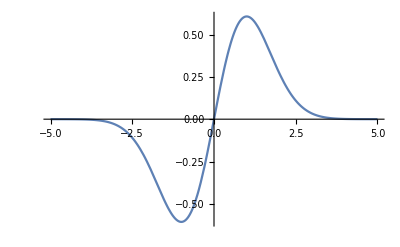

```mathematica
Plot[(ⅇ^((-(-a+x)^2)/2)-ⅇ^((-(a^2+x^2))/2))/(√(1-ⅇ^(-a^2))),{x,-5,5},PlotRange->All]
a:=0.0001
```

```mathematica
(k^2*Pi)^(-1/4)Limit[(Exp[-1/2*((x-a)/k)^2]-Exp[-1/2*(x/k)^2]*Exp[-a^2/2])/Sqrt[1-ⅇ^(-a^2)],a->0]
```

(ⅇ^(-x^2/(2 k^2)) x)/((k^2)^(5/4) π^(1/4))

```mathematica
Integrate[((ⅇ^(-x^2/(2 k^2)) x)/((k^2)^(5/4) π^(1/4))Sqrt[2])^2,{x,-Infinity,Infinity}]
```

ConditionalExpression[(√(1/k^2))/(√(k^2)),Re[1/k^2]>0]